New in CIP 1.1

QSPR with MLR

This tutorial demonstrates new functions of CIP version 1.1 that complement the discussion in textbook

Achim Zielesny, From Curve Fitting to Machine Learning: An illustrative Guide to scientific Data Analysis and Computational Intelligence, Berlin 2011. (Springer: Intelligent Systems Reference Library, Volume 18).

CIP is available at http://www.gnwi.de.

```mathematica
Clear["Global`*"];
<<CIP`Utility`
<<CIP`ExperimentalData`
<<CIP`DataTransformation`
<<CIP`Graphics`
<<CIP`Cluster`
<<CIP`MLR`
```

A Quantitative Structure-Property Relationsship (QSPR) is a model that maps features of chemical structures or reactions (the input) to a quantity of interest (the output). The features of a chemical structure or reaction are so called (structural/molecular) descriptors, i.e. characteristic numbers which are calculated for the specific structure/reaction. The output quantity of interest is usually measured experimentally. QSPR models may be constructed with machine learning approaches.

The following QSPR data set comprises 2169 input/output (I/O) pairs that each represent a single chemical reaction. Each input vector consists of 130 components where each component is a calculated structural descriptor. Each corresponding output vector contains a single experimentally measured value for a reaction-related physico-chemical quantity.

```mathematica
dataSet=CIP`ExperimentalData`GetQSPRDataSet02[];
CIP`Graphics`ShowDataSetInfo[{"IoPairs","InputComponents","OutputComponents"},dataSet]
```

Number of IO pairs = 2169

Number of input components = 130

Number of output components = 1

An initial k-medoids clustering analysis of the data set's input vectors leads to two clusters on the basis of a mean silhouette width decision

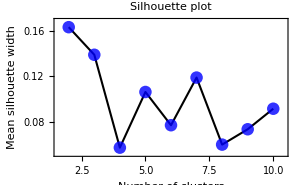

```mathematica
inputs=CIP`Utility`GetInputsOfDataSet[dataSet];
minimumNumberOfClusters=2;
maximumNumberOfClusters=10;
silhouettePlotPoints=CIP`Cluster`GetSilhouettePlotPoints[inputs,minimumNumberOfClusters,maximumNumberOfClusters];
CIP`Cluster`ShowSilhouettePlot[silhouettePlotPoints]
```

with a mean silhouette width of only 0.16 which signals a mostly non-structured uniform distribution of the data in the input space - a feature that is desired for the following supervised regression task. To quantitatively model the relationship between the reaction descriptors and the corresponding physico-chemical quantity a linear method (MLR - Multiple Linear Regression) is initially used:

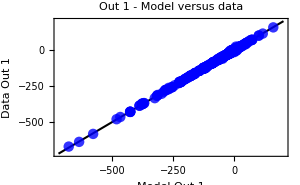

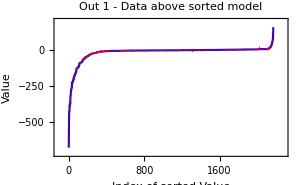

Out 1 : Correlation coefficient = 0.999373

```mathematica
mlrInfo=CIP`MLR`FitMlr[dataSet];
pointSize=0.025;
CIP`MLR`ShowMlrSingleRegression[{"ModelVsDataPlot","SortedModelVsDataPlot","CorrelationCoefficient"},dataSet,mlrInfo,GraphicsOptionPointSize->pointSize];
```

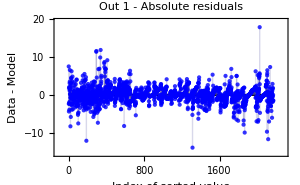

Definition of 'Residual (absolute)': Data - Model

Out 1 : Residual (absolute): Mean/Median/Maximum Value = 1.4 / 9.84×10^-1 / 1.79×10^1

Root mean squared error (RMSE) = 2.063

```mathematica
pointSize=0.01;
CIP`MLR`ShowMlrSingleRegression[{"AbsoluteSortedResidualsPlot","AbsoluteResidualsStatistics","RMSE"},dataSet,mlrInfo,GraphicsOptionPointSize->pointSize];
```

The linear model already achieves an excellent description of the data with a root mean squared error (RMSE) of 2.06 and a (Pearson) correlation coefficient of practically 1 (0.9994). Unlike the non-linear machine learning methods (e.g. neural networks or support vector machines) MLR is not prone to overfitting due to its linear nature (a hyperplane is a priori imposed as the structural form). But this fact alone does not bail for the desired predictive value of the model. To assure that the MLR result is not only a mere data representation but a true predictive model the whole data are partitioned into a training and a test set of equal size with the MLR approach repeated on the training and validated on the test set. To obtain training and test data that cover a similar input space with a similar spatial diversity (a desired feature to assure that the model is predictive on the whole range of inputs) in combination with a maximum predictive training set so called cluster representatives are evaluated in a first step. These representatives are then refined by an iterative procedure that exchanges data between training and test set that belong to the same cluster. The latter constraint assures that the input data of training and test set maintain a similar spatial diversity. A single iteration determines the test set I/O pair with the largest deviation between data and model. This I/O pair is then transferred to the training set while the best predicted I/O pair of the same cluster in the training set is transferred to the test set in exchange. Oscillations during the refinement steps are suppressed by blacklisting exchanged I/O pairs:

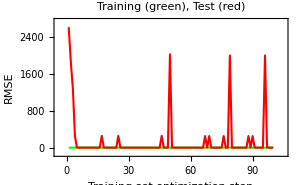

```mathematica
trainingFraction=0.5;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=20;
mlrTrainOptimization=CIP`MLR`GetMlrTrainOptimization[dataSet,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength->blackListLength];
CIP`MLR`ShowMlrTrainOptimization[mlrTrainOptimization];
```

```mathematica
bestOptimization="MinimumDeviation";
bestRegressionStep=CIP`MLR`GetBestMlrRegressOptimization[mlrTrainOptimization,UtilityOptionsBestOptimization->bestOptimization]
```

55

Training Set:

Root mean squared error (RMSE) = 2.185

Out 1 : Root mean squared error (RMSE) = 2.185

Definition of 'Residual (absolute)': Data - Model

Out 1 : Residual (absolute): Mean/Median/Maximum Value = 1.51 / 1.11 / 1.36×10^1

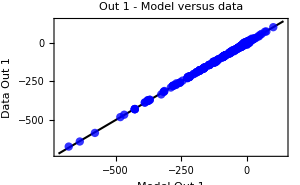

Out 1 : Correlation coefficient = 0.999603

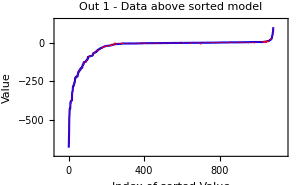

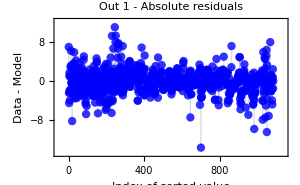

Test Set:

Root mean squared error (RMSE) = 2.189

Out 1 : Root mean squared error (RMSE) = 2.189

Definition of 'Residual (absolute)': Data - Model

Out 1 : Residual (absolute): Mean/Median/Maximum Value = 1.45 / 1.1 / 3.05×10^1

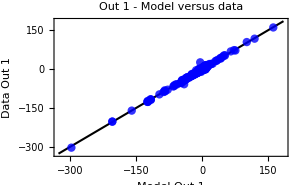

Out 1 : Correlation coefficient = 0.995208

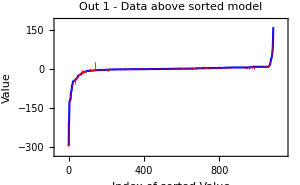

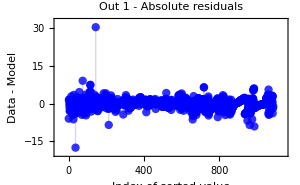

```mathematica
trainingAndTestSetList=mlrTrainOptimization[[3]];
mlrInfoList=mlrTrainOptimization[[4]];
trainingAndTestSet=trainingAndTestSetList[[bestRegressionStep]];
bestMlrInfo=mlrInfoList[[bestRegressionStep]];
pointSize=0.02;
CIP`MLR`ShowMlrRegressionResult[{"RMSE","SingleOutputRMSE","AbsoluteResidualsStatistics","ModelVsDataPlot","CorrelationCoefficient","SortedModelVsDataPlot","AbsoluteSortedResidualsPlot"},trainingAndTestSet,bestMlrInfo,GraphicsOptionPointSize->pointSize]
```

For the data set in question the sketched splitting procedure leads to a training and test set with a RMSE value of 2.19 for both sets which is in close proximity to the value of 2.06 obtained for the MLR analysis of the whole data set. In summary it can be claimed that the MLR approach leads to a convincing and predictive model for the QSPR task in question. An extension of the analysis towards non-linear machine learning methods is not advised.